```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues/gpls/positive"];
ViewSurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
plot1=ListPlot3D[data,BoxRatios->Automatic];
plot2=ListPlot[Transpose[Drop[Transpose[data],-1]], PlotRange->{{ 0, 500}, {-500, 500}}];
{plot1,plot2}
]
files= FileNames[];
numbersInString[s_]:=ToExpression@StringCases[s,NumberString]
files = SortBy[files,numbersInString]
allPlots=Table[ViewSurface[file],{file,files}];
(*ListAnimate[allPlots]*)
```

{surface0positive.gpl,surface1positive.gpl,surface2positive.gpl,surface3positive.gpl,surface4positive.gpl,surface5positive.gpl,surface6positive.gpl,surface7positive.gpl,surface8positive.gpl,surface9positive.gpl,surface10positive.gpl,surface11positive.gpl,surface12positive.gpl,surface13positive.gpl,surface14positive.gpl,surface15positive.gpl,surface16positive.gpl,surface17positive.gpl,surface18positive.gpl,surface19positive.gpl,surface20positive.gpl,surface21positive.gpl,surface22positive.gpl,surface23positive.gpl,surface24positive.gpl,surface25positive.gpl,surface26positive.gpl,surface27positive.gpl,surface28positive.gpl,surface29positive.gpl,surface30positive.gpl,surface31positive.gpl,surface32positive.gpl,surface33positive.gpl,surface34positive.gpl,surface35positive.gpl,surface36positive.gpl,surface37positive.gpl,surface38positive.gpl,surface39positive.gpl,surface40positive.gpl,surface41positive.gpl,surface42positive.gpl,surface43positive.gpl,surface44positive.gpl,surface45positive.gpl,surface46positive.gpl,surface47positive.gpl,surface48positive.gpl,surface49positive.gpl,surface50positive.gpl,surface51positive.gpl,surface52positive.gpl,surface53positive.gpl,surface54positive.gpl,surface55positive.gpl,surface56positive.gpl,surface57positive.gpl,surface58positive.gpl,surface59positive.gpl,surface60positive.gpl,surface61positive.gpl,surface62positive.gpl,surface63positive.gpl,surface64positive.gpl,surface65positive.gpl,surface66positive.gpl,surface67positive.gpl,surface68positive.gpl,surface69positive.gpl,surface70positive.gpl,surface71positive.gpl,surface72positive.gpl,surface73positive.gpl,surface74positive.gpl,surface75positive.gpl,surface76positive.gpl,surface77positive.gpl,surface78positive.gpl,surface79positive.gpl,surface80positive.gpl,surface81positive.gpl,surface82positive.gpl,surface83positive.gpl,surface84positive.gpl,surface85positive.gpl,surface86positive.gpl,surface87positive.gpl,surface88positive.gpl,surface89positive.gpl,surface90positive.gpl,surface91positive.gpl,surface92positive.gpl,surface93positive.gpl,surface94positive.gpl,surface95positive.gpl,surface96positive.gpl,surface97positive.gpl,surface98positive.gpl,surface99positive.gpl,surface100positive.gpl,surface101positive.gpl,surface102positive.gpl,surface103positive.gpl,surface104positive.gpl,surface105positive.gpl,surface106positive.gpl,surface107positive.gpl,surface108positive.gpl,surface109positive.gpl,surface110positive.gpl,surface111positive.gpl,surface112positive.gpl,surface113positive.gpl,surface114positive.gpl,surface115positive.gpl,surface116positive.gpl,surface117positive.gpl,surface118positive.gpl,surface119positive.gpl,surface120positive.gpl,surface121positive.gpl,surface122positive.gpl,surface123positive.gpl,surface124positive.gpl,surface125positive.gpl,surface126positive.gpl,surface127positive.gpl,surface128positive.gpl,surface129positive.gpl,surface130positive.gpl,surface131positive.gpl,surface132positive.gpl,surface133positive.gpl,surface134positive.gpl,surface135positive.gpl,surface136positive.gpl,surface137positive.gpl,surface138positive.gpl,surface139positive.gpl,surface140positive.gpl,surface141positive.gpl,surface142positive.gpl,surface143positive.gpl,surface144positive.gpl,surface145positive.gpl,surface146positive.gpl,surface147positive.gpl,surface148positive.gpl,surface149positive.gpl,surface150positive.gpl,surface151positive.gpl,surface152positive.gpl,surface153positive.gpl,surface154positive.gpl,surface155positive.gpl,surface156positive.gpl,surface157positive.gpl,surface158positive.gpl,surface159positive.gpl,surface160positive.gpl,surface161positive.gpl,surface162positive.gpl,surface163positive.gpl,surface164positive.gpl,surface165positive.gpl,surface166positive.gpl,surface167positive.gpl,surface168positive.gpl,surface169positive.gpl,surface170positive.gpl}

{{50,237.225},{60,208.424},{70,182.825},{80,162.276},{90,145.178},{100,132.664},{110,121.904},{120,114.068},{130,106.592},{140,101.156},{150,96.162},{160,91.8261},{170,88.4617},{180,85.1918},{190,82.5191},{200,77.2738},{210,76.5923},{220,75.4269},{230,73.1237},{240,71.2169},{250,69.351},{260,67.1341},{270,56.0835},{280,67.0511},{290,65.0221},{300,63.5094},{310,62.0634},{320,60.021},{330,61.4446},{340,59.191},{350,63.4139},{360,55.3694},{370,57.8114},{380,56.5185},{390,55.5913},{400,54.7636},{410,53.9947},{420,53.2695},{430,52.5806},{440,51.9233},{450,51.2944},{460,50.6916},{470,50.1129},{480,49.5568},{490,49.0219},{500,48.5071},{510,48.0112},{520,47.5335},{530,47.0729},{540,46.6287},{550,46.2003},{560,45.7868},{570,45.3877},{580,45.0024},{590,44.6303},{600,44.271},{610,43.9238},{620,43.5884},{630,43.2643},{640,42.9512},{650,42.6485},{660,42.356},{670,42.0732},{680,41.7999},{690,41.5356},{700,41.2802},{710,41.0333},{720,40.7946},{730,40.5639},{740,40.3408},{750,40.1252},{760,39.9169},{770,39.7155},{780,39.5209},{790,39.3328},{800,39.1512},{810,38.9757},{820,38.8062},{830,38.6426},{840,38.4846},{850,38.3321},{860,38.1849},{870,38.0429},{880,37.906},{890,37.774},{900,37.6467},{910,37.5241},{920,37.4061},{930,37.2925},{940,37.1831},{950,37.078},{960,36.9769},{970,36.8799},{980,36.7867},{990,36.6974},{1000,36.6117},{1010,36.5297},{1020,36.4512},{1030,36.3762},{1040,36.3046},{1050,36.2363},{1060,36.1712},{1070,36.1093},{1080,36.0505},{1090,35.9948},{1100,35.942},{1110,35.8922},{1120,35.8452},{1130,35.801},{1140,35.7595},{1150,35.7207},{1160,35.6846},{1170,35.6511},{1180,35.62},{1190,35.5915},{1200,35.5654},{1210,35.5417},{1220,35.5204},{1230,35.5013},{1240,35.4845},{1250,35.4699},{1260,35.4574},{1270,35.447},{1280,35.4388},{1290,35.4325},{1300,35.4282},{1310,35.4258},{1320,35.4253},{1330,35.4267},{1340,35.4298},{1350,35.4347},{1360,35.4412},{1370,35.4494},{1380,35.4592},{1390,35.4706},{1400,35.4834},{1410,35.4977},{1420,35.5135},{1430,35.5306},{1440,35.549},{1450,35.5687},{1460,35.5897},{1470,35.612},{1480,35.6355},{1490,35.6603},{1500,35.6864},{1510,35.7139},{1520,35.7429},{1530,35.7736},{1540,35.8063},{1550,35.8414},{1560,35.8796},{1570,35.9219},{1580,35.97},{1590,36.0268},{1600,36.0978},{1610,36.1952},{1620,36.3545},{1630,36.8164},{1640,33.8417},{1650,40.385},{1660,35.7213},{1670,36.9123},{1680,34.7214},{1690,35.6325},{1700,35.953},{1710,36.2808},{1720,37.0178},{1730,25.9586},{1740,34.7046},{1750,35.4055}}

{{50,0.00237225},{60,0.00208424},{70,0.00182825},{80,0.00162276},{90,0.00145178},{100,0.00132664},{110,0.00121904},{120,0.00114068},{130,0.00106592},{140,0.00101156},{150,0.00096162},{160,0.000918261},{170,0.000884617},{180,0.000851918},{190,0.000825191},{200,0.000772738},{210,0.000765923},{220,0.000754269},{230,0.000731237},{240,0.000712169},{250,0.00069351},{260,0.000671341},{270,0.000560835},{280,0.000670511},{290,0.000650221},{300,0.000635094},{310,0.000620634},{320,0.00060021},{330,0.000614446},{340,0.00059191},{350,0.000634139},{360,0.000553694},{370,0.000578114},{380,0.000565185},{390,0.000555913},{400,0.000547636},{410,0.000539947},{420,0.000532695},{430,0.000525806},{440,0.000519233},{450,0.000512944},{460,0.000506916},{470,0.000501129},{480,0.000495568},{490,0.000490219},{500,0.000485071},{510,0.000480112},{520,0.000475335},{530,0.000470729},{540,0.000466287},{550,0.000462003},{560,0.000457868},{570,0.000453877},{580,0.000450024},{590,0.000446303},{600,0.00044271},{610,0.000439238},{620,0.000435884},{630,0.000432643},{640,0.000429512},{650,0.000426485},{660,0.00042356},{670,0.000420732},{680,0.000417999},{690,0.000415356},{700,0.000412802},{710,0.000410333},{720,0.000407946},{730,0.000405639},{740,0.000403408},{750,0.000401252},{760,0.000399169},{770,0.000397155},{780,0.000395209},{790,0.000393328},{800,0.000391512},{810,0.000389757},{820,0.000388062},{830,0.000386426},{840,0.000384846},{850,0.000383321},{860,0.000381849},{870,0.000380429},{880,0.00037906},{890,0.00037774},{900,0.000376467},{910,0.000375241},{920,0.000374061},{930,0.000372925},{940,0.000371831},{950,0.00037078},{960,0.000369769},{970,0.000368799},{980,0.000367867},{990,0.000366974},{1000,0.000366117},{1010,0.000365297},{1020,0.000364512},{1030,0.000363762},{1040,0.000363046},{1050,0.000362363},{1060,0.000361712},{1070,0.000361093},{1080,0.000360505},{1090,0.000359948},{1100,0.00035942},{1110,0.000358922},{1120,0.000358452},{1130,0.00035801},{1140,0.000357595},{1150,0.000357207},{1160,0.000356846},{1170,0.000356511},{1180,0.0003562},{1190,0.000355915},{1200,0.000355654},{1210,0.000355417},{1220,0.000355204},{1230,0.000355013},{1240,0.000354845},{1250,0.000354699},{1260,0.000354574},{1270,0.00035447},{1280,0.000354388},{1290,0.000354325},{1300,0.000354282},{1310,0.000354258},{1320,0.000354253},{1330,0.000354267},{1340,0.000354298},{1350,0.000354347},{1360,0.000354412},{1370,0.000354494},{1380,0.000354592},{1390,0.000354706},{1400,0.000354834},{1410,0.000354977},{1420,0.000355135},{1430,0.000355306},{1440,0.00035549},{1450,0.000355687},{1460,0.000355897},{1470,0.00035612},{1480,0.000356355},{1490,0.000356603},{1500,0.000356864},{1510,0.000357139},{1520,0.000357429},{1530,0.000357736},{1540,0.000358063},{1550,0.000358414},{1560,0.000358796},{1570,0.000359219},{1580,0.0003597},{1590,0.000360268},{1600,0.000360978},{1610,0.000361952},{1620,0.000363545},{1630,0.000368164},{1640,0.000338417},{1650,0.00040385},{1660,0.000357213},{1670,0.000369123},{1680,0.000347214},{1690,0.000356325},{1700,0.00035953},{1710,0.000362808},{1720,0.000370178},{1730,0.000259586},{1740,0.000347046},{1750,0.000354055}}

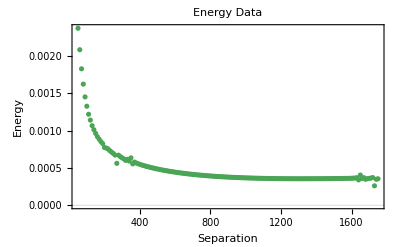

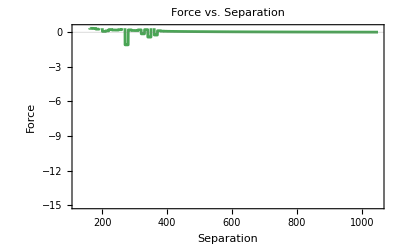

```mathematica
SolveForce[filename_] :=
Module[{stream, data,force, forcefunction, forceplot, x},
stream = OpenRead[filename];
data = ReadList[stream,{Number,Number}];
Close[stream];
data
];
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues"];
Print[SolveForce["energysep.txt"]];
allData=SolveForce["energysep.txt"];
{sep, energy}= Transpose[allData];
showData = Transpose[{sep,Map[#/(10^5)&,energy//N]}]
energyGraph = ListPlot[showData, PlotRange->All, PlotLabel->"Energy Data", PlotTheme->"Scientific", AxesLabel->{"Separation", "Energy"}, PlotStyle->Darker[Blend[{Green, LightBlue}]]]
(*ListPlot[allData,Joined->True]*)
force[x_]=-D[Interpolation[allData,InterpolationOrder->1][x],x];
forceGraph = Plot[force[x],{x,150, 1050},PlotTheme->"Scientific", AxesLabel->{"Separation", "Force"}, AxesOrigin->{125,-15}, PlotLabel->"Force vs. Separation", PlotStyle->{{Thickness[0.005],Darker[Blend[{Green, LightBlue}]]}}]
SetDirectory[StringJoin[NotebookDirectory[],"gpls/"]];
```

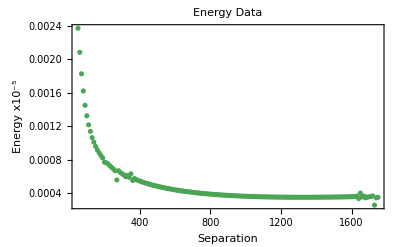

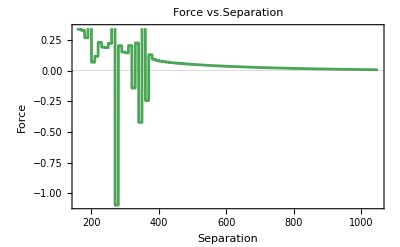

```mathematica
energyGraphnice = Show[energyGraph,AxesLabel->{None,None},FrameLabel->{{HoldForm[Energy x10^("-5")],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Energy Data],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full,  PlotRange->All]
forceGraphnice = Show[forceGraph,AxesLabel->{None,None},FrameLabel->{{HoldForm[Force],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Force vs. Separation],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full, PlotRange->All]
```

```mathematica
Close[stream];
```

```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues/gpls/positive"];
prettySurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
colorScheme = ColorData["DarkRainbow"];
prettyData=ListPlot3D[data,Mesh->20, InterpolationOrder->3,ColorFunction->Function[{x, y, z},colorScheme[z]],BoxRatios->{Automatic,Automatic,100}, PlotStyle->Opacity[.9], Boxed->False, Axes->False, Background->None];
prettyData
]
prettySurface["surface60positive.gpl"]
Show[prettySurface["surface100positive.gpl"],ViewPoint->Front]
```

-Graphics3D-

-Graphics3D-

```mathematica
prettySurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
colorScheme = ColorData["DarkRainbow"];
prettyData=ListPlot3D[data,Mesh->10, InterpolationOrder->3,ColorFunction->Function[{x, y, z},colorScheme[z]],BoxRatios->Automatic, PlotStyle->Opacity[.9], Boxed->False, Axes->False, Background->None,PlotRange->{{-300,300},{-150,150},Automatic}];
Show[prettyData,Graphics3D[{Black,Sphere[{137.5,0,400},10],Cylinder[{{-137.5,0,399},{-137.5,0,401}},10]}]]
]
prettySurface["surface16positive.gpl"]
```

-Graphics3D-

```mathematica
|
```